```mathematica
starttime={1990};
endtime = {2021};
city = "Sokal";
```

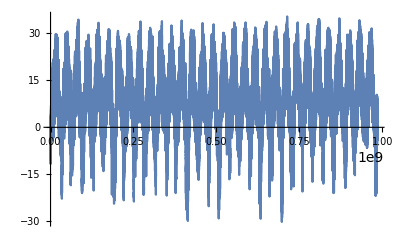

```mathematica
station = WeatherData[city];
entity = "Temperature";
temp = WeatherData[station,entity,{starttime,endtime}];
abstime = AbsoluteTime/@temp["Dates"]-AbsoluteTime[starttime];
templist = temp["Values"]/.Missing["NotAvailable"]->8.2+RandomReal[{-3,3}];
tempabs = {abstime,templist};
ListPlot[
Transpose[tempabs],
Joined->True
]
```

```mathematica
Export[NotebookDirectory[]<>"\\" <> ToString[station] <> "_"<>entity<>"_from_"<>ToString[First[starttime]]<>"_to_"<>ToString[First[endtime]]<>".mat",tempabs];
```

```mathematica
coordinates = CityData[city,"Coordinates"]
```

{50.48,24.28}

```mathematica
Rx:=RotationMatrix[#,{1,0,0}]&;
Ry:=RotationMatrix[#,{0,1,0}]&;
Rz:=RotationMatrix[#,{0,0,1}]&;
R:=Rx[Pi/2-#2[[1]]].Rz[2 #1 Pi].Rx[#2[[2]]].Rz[(2 #1 Pi)/365-Pi/2]&;
Rmax:=Rx[Pi/2-#2[[1]]].Rz[(366 2 #1)/365-Pi].Rx[#2[[2]]].Rz[Pi/2]&;
```

```mathematica
Manipulate[Graphics3D[Tube[{Rx[Pi/2-coordinates[[1]]].Rz[2θ Pi ].Rx[Pi/2-axialtilt].Rz[(2θ Pi)/365].{1,0,0},{0,0,0}}],PlotRange->{{-1,1},{-1,1},{-1,1}}],{θ,0,365}]
```

Part::partd: Part specification coordinates⟦1⟧ is longer than depth of object.